```mathematica
ClearAll["Global`*"];
```

```mathematica
Subscript[λ, 1]=2;Subscript[λ, 2]=3;
D1=GammaDistribution[3/2,1/Subscript[λ, 1]];
D2=GammaDistribution[3/2,1/Subscript[λ, 2]];
(*D1=ProbabilityDistribution[4 ⅇ^(-2 x) √(2/π) √x,{x,0,10}];
D2=ProbabilityDistribution[6 ⅇ^(-3 x) √(3/π) √x,{x,0,10}];*)
PDF[D1,x]
PDF[D2,x]
```

Piecewise[{{4 ⅇ^(-2 x) √(2/π) √x, x>0}, {0, True}}]

Piecewise[{{6 ⅇ^(-3 x) √(3/π) √x, x>0}, {0, True}}]

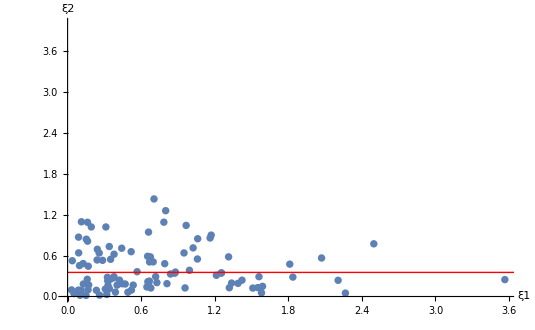

```mathematica
ξ1=RandomVariate[D1,100];
ξ2=RandomVariate[D2,100];
fξ1[x1_]:=√((2x1)/Pi)Subscript[λ, 1]^(3/2)E^(-Subscript[λ, 1]x1);
fξ2[x2_]:=√((2x2)/Pi)Subscript[λ, 2]^(3/2)E^(-Subscript[λ, 2]x2);
Fξ1[x1_]:=Integrate[fξ1[x],{x,0,x1}];
Fξ2[x2_]:=Integrate[fξ2[x],{x,0,x2}];
ξ={{ξ1[[1]],ξ2[[1]]}};

For[i=2,i≤100,i++,ξ=Append[ξ,{ξ1[[i]],ξ2[[i]]}]];
line=Integrate[x fξ2[x],{x,0,Infinity}];
Show[ListPlot[ξ,PlotRange->{0,4},AxesLabel->{"ξ1","ξ2"},PlotStyle->PointSize[0.01]],Plot[line,{x,0,4},PlotStyle->{Thick,Red}]]
```

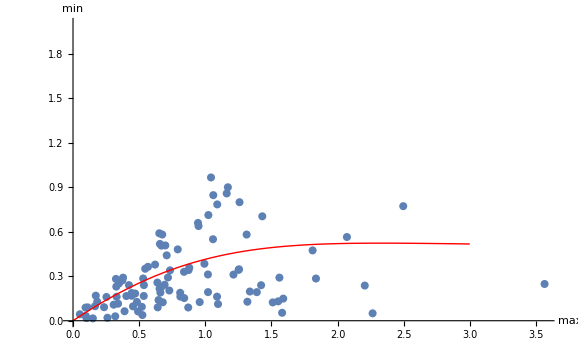

```mathematica
ξmaxmin={{Max[ξ1[[1]],ξ2[[1]]],Min[ξ1[[1]],ξ2[[1]]]}};
For[i=2,i≤100,i++,ξmaxmin=Append[ξmaxmin,{Max[ξ1[[i]],ξ2[[i]]],Min[ξ1[[i]],ξ2[[i]]]}]];

fmax=fξ1[x2]Fξ2[x2]+fξ2[x2]Fξ1[x2];
fminmax=fξ1[x1]fξ2[x2]+fξ1[x2]fξ2[x1];
R=1/fmax Integrate[x1 fminmax,{x1,0,x2}];
Show[ListPlot[ξmaxmin,PlotRange->{0,2},AxesLabel->{"max","min"},PlotStyle->PointSize[0.01]],Plot[R,{x2,0,3},PlotStyle->{Thick,Red}]]
```

```mathematica
ξ
```

{{1.58124,0.0535892},{0.319303,0.0297622},{0.403457,0.166663},{0.12674,0.483396},{0.234794,0.091427},{0.327272,0.230277},{2.07107,0.564907},{0.652493,0.590108},{0.0322429,0.0965973},{1.81163,0.47457},{0.372973,0.272384},{0.260361,0.0199651},{0.347609,0.251895},{0.791901,0.48146},{0.95787,0.125827},{0.307397,0.108243},{0.378344,0.290628},{0.150017,0.0159342},{0.566821,0.363868},{1.16212,0.858916},{0.654463,0.217035},{0.423001,0.240196},{0.878919,0.358259},{1.38973,0.192848},{0.660044,0.945132},{0.520472,0.0938374},{0.949216,0.639051},{0.443501,0.187094},{0.727986,0.20399},{0.168356,0.444256},{0.339953,0.733508},{0.193053,1.02081},{0.441215,0.708387},{0.10163,0.0177773},{0.518394,0.657277},{0.166511,0.0980465},{0.668328,0.506923},{0.71796,0.291807},{0.966848,1.04338},{0.491751,0.0625489},{0.67471,0.581692},{0.0517196,0.0436311},{0.0383168,0.524674},{0.340848,0.115118},{1.25541,0.347042},{1.17094,0.900798},{0.66064,0.190061},{1.33725,0.197138},{0.242645,0.692661},{0.6979,0.508116},{0.799854,1.25908},{0.535013,0.167147},{0.16288,0.811751},{0.162425,1.08919},{0.329692,0.161891},{2.20608,0.237396},{0.785034,1.09052},{2.26544,0.0499102},{1.5103,0.123611},{2.49693,0.773118},{0.378781,0.620497},{1.02355,0.713165},{0.160238,0.252756},{1.55144,0.130753},{0.993577,0.384287},{0.172236,0.169244},{1.05855,0.550017},{0.31216,1.02022},{0.469614,0.183299},{1.06079,0.847474},{1.56064,0.290771},{1.5897,0.149214},{0.704707,1.43108},{0.0903043,0.640151},{0.0969306,0.453496},{0.0893893,0.871151},{0.678768,0.124518},{1.21329,0.31133},{0.25764,0.637984},{1.31279,0.581556},{1.31859,0.128223},{0.839196,0.329888},{1.8369,0.284828},{0.64668,0.139545},{0.32467,0.282095},{3.56561,0.24803},{0.873916,0.341817},{0.350618,0.545695},{0.810409,0.188641},{0.240494,0.536034},{0.0886124,0.0947378},{0.666511,0.226127},{1.42228,0.239593},{0.112584,1.0964},{1.25166,0.343191},{0.38975,0.0639346},{0.285171,0.530588},{0.1109,0.0901051},{0.152917,0.840782},{0.128641,0.183114}}

```mathematica
ξmaxmin
```

{{1.58124,0.0535892},{0.319303,0.0297622},{0.403457,0.166663},{0.483396,0.12674},{0.234794,0.091427},{0.327272,0.230277},{2.07107,0.564907},{0.652493,0.590108},{0.0965973,0.0322429},{1.81163,0.47457},{0.372973,0.272384},{0.260361,0.0199651},{0.347609,0.251895},{0.791901,0.48146},{0.95787,0.125827},{0.307397,0.108243},{0.378344,0.290628},{0.150017,0.0159342},{0.566821,0.363868},{1.16212,0.858916},{0.654463,0.217035},{0.423001,0.240196},{0.878919,0.358259},{1.38973,0.192848},{0.945132,0.660044},{0.520472,0.0938374},{0.949216,0.639051},{0.443501,0.187094},{0.727986,0.20399},{0.444256,0.168356},{0.733508,0.339953},{1.02081,0.193053},{0.708387,0.441215},{0.10163,0.0177773},{0.657277,0.518394},{0.166511,0.0980465},{0.668328,0.506923},{0.71796,0.291807},{1.04338,0.966848},{0.491751,0.0625489},{0.67471,0.581692},{0.0517196,0.0436311},{0.524674,0.0383168},{0.340848,0.115118},{1.25541,0.347042},{1.17094,0.900798},{0.66064,0.190061},{1.33725,0.197138},{0.692661,0.242645},{0.6979,0.508116},{1.25908,0.799854},{0.535013,0.167147},{0.811751,0.16288},{1.08919,0.162425},{0.329692,0.161891},{2.20608,0.237396},{1.09052,0.785034},{2.26544,0.0499102},{1.5103,0.123611},{2.49693,0.773118},{0.620497,0.378781},{1.02355,0.713165},{0.252756,0.160238},{1.55144,0.130753},{0.993577,0.384287},{0.172236,0.169244},{1.05855,0.550017},{1.02022,0.31216},{0.469614,0.183299},{1.06079,0.847474},{1.56064,0.290771},{1.5897,0.149214},{1.43108,0.704707},{0.640151,0.0903043},{0.453496,0.0969306},{0.871151,0.0893893},{0.678768,0.124518},{1.21329,0.31133},{0.637984,0.25764},{1.31279,0.581556},{1.31859,0.128223},{0.839196,0.329888},{1.8369,0.284828},{0.64668,0.139545},{0.32467,0.282095},{3.56561,0.24803},{0.873916,0.341817},{0.545695,0.350618},{0.810409,0.188641},{0.536034,0.240494},{0.0947378,0.0886124},{0.666511,0.226127},{1.42228,0.239593},{1.0964,0.112584},{1.25166,0.343191},{0.38975,0.0639346},{0.530588,0.285171},{0.1109,0.0901051},{0.840782,0.152917},{0.183114,0.128641}}

```mathematica
n={{0,0}};
For[i=1,i≤100,i++,
If [Fξ1[ξ1[[i]]]*Fξ2[ξ2[[i]]]≥0.1,n = Append[n,{Fξ1[ξ1[[i]]],Fξ2[ξ2[[i]]]}]];
]
```

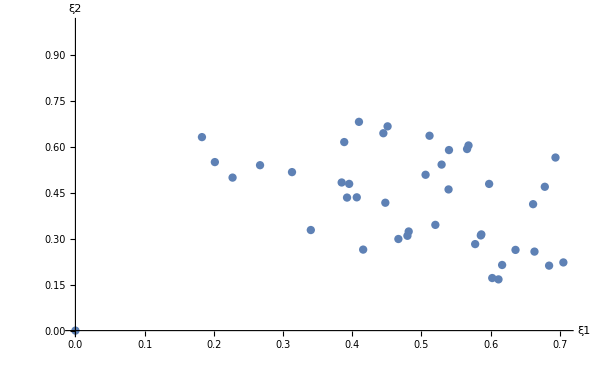

```mathematica
ListPlot[n,PlotRange->{0,1},AxesLabel->{"ξ1","ξ2"},PlotStyle->PointSize[0.01]]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
InverseFourierTransform[((1 2)/((1-I t)(2-I t)))^(3/2),t,x,Assumptions ->{ x≥0,λ1≥0,λ2≥0,t≥0}]
```

InverseFourierTransform[2 √2 (1/((1-ⅈ t) (2-ⅈ t)))^(3/2),t,x,Assumptions→{x≥0,λ1≥0,λ2≥0,t≥0}]

```mathematica
InverseFourierTransform[(λ1/(λ1-I t))^(3/2),t,x,Assumptions ->{ x≥0,λ1≥0,λ2≥0,t≥0}]
$Aborted
```

2 √2 ⅇ^(-x λ1) √(x λ1^3)

$Aborted

```mathematica
Integrate[6  √(3/π)√(2/π)  √(x(z-x))4 E^(x-3z),{x,0,z}]
```

∫_0^z (24 √6 ⅇ^(x-3 z) √(x (-x+z)))/π ⅆx